```mathematica
(*1. Ellenőrizzük a (2)-(5) egyenleteket. *)

(* 2 *)Simplify[Integrate[Sin[n*Pi*x/a]*Sin[m*Pi*x/a],{x,-a,a}],Element[{m,n},Integers]]
(* 2 *)Simplify[Integrate[Sin[n*Pi*x/a]*Sin[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]

(* 3 *)Simplify[Integrate[Sin[n*Pi*x/a]*Cos[m*Pi*x/a],{x,-a,a}],Element[{m,n},Integers]]

(* 4 *)Simplify[Integrate[Sin[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]
(* 5 *)Simplify[Integrate[Cos[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]
```

0

a

0

0

0

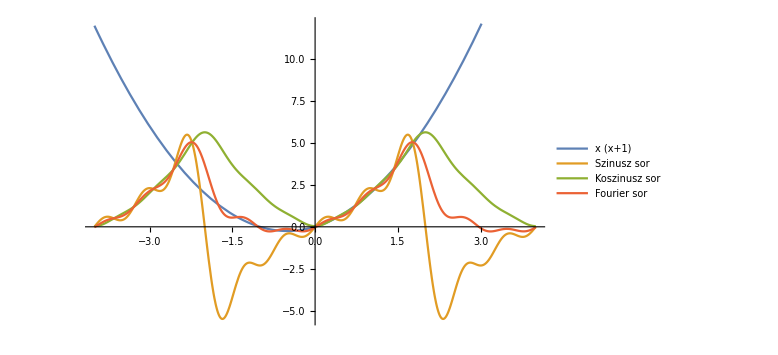

```mathematica
(*2.a.*)
fourierSinCoefficient[f_,x_,m_,a_] := 2/a* Integrate[f*Sin[m*Pi*x/a], {x, 0, a}]

(*2.b.*)
fourierCosCoefficient[f_,x_,m_,a_] :=If[m==0,1/a*Integrate[f,{x, 0, a}],2/a* Integrate[f*Cos[m*Pi*x/a], {x, 0, a}]]



fourierTrigCoefficient[f_,x_,m_,a_,sc_]:=
If[sc==0,
If[m==0, 1/2/a*Integrate[f,{x,-a,a}],
1/a*Integrate[f*Cos[m*Pi*x/a],{x,-a,a}]
],
1/a*Integrate[f*Sin[m*Pi*x/a],{x,-a,a}]
];

(*2.c. *)
f[x_] = x(x+1);

fsin[f_,x_]=Sum[fourierSinCoefficient[f[x], x, n, 2]*Sin[n*Pi*x/2], {n, 0, 5}];
fcos[f_,x_]=Sum[fourierCosCoefficient[f[x], x, n, 2]*Cos[n*Pi*x/2], {n, 0, 5}];
ffourier[f_,x_]=Sum[fourierTrigCoefficient[f[x], x, n, 2, 0]*Cos[n*Pi*x/2]+fourierTrigCoefficient[f[x], x, n, 2, 1]*Sin[n*Pi*x/2], {n,0,5}];

Plot[{
f[x],
fsin[f,x],
fcos[f,x],
ffourier[f,x]
}, {x, -4, 4},
PlotLegends->{f[x],"Szinusz sor", "Koszinusz sor","Fourier sor" },
ImageSize->Large
]
```

```mathematica
(*3. feladat *)
sol3=DSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}],
u[0,x]==x*(1-x),
u[t,0]==0,
u[t,1]==0},u,{t,x}]/.{Infinity->10}//Activate;
plotSol3=Plot3D[sol3[t,x],{t,0,0.5},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];
```

```mathematica
g[x_]=x(1-x);
u3=Sum[fourierSinCoefficient[g,x,n,1]  * Sin[n*Pi*x]*Exp[-(n*Pi)^2*t],{n,1,10}];
plotU3=Plot3D[u3,{t,0,0.5},{x,0,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];
Show[plotSol3, plotU3]
```

-Graphics3D-

```mathematica
(*4. Feladat *)
g4[x_]:=x(1-x);
f4[t_,x_]:=t^2*x*(1-x);
a=1;
(*fn4[t,n]*)

u4=Sum[
DSolveValue[
{u'[t]+Pi^2*n^2*u[t]==fourierSinCoefficient[f4[t,x],x,n,1],
u[0]==fourierSinCoefficient[g4[x],x,n,1]},
u[t],t]* Sin[n*Pi*x],
{n,1,10}];

plotU4=Plot3D[u4,{t,0,5},{x,0,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];

sol4=DSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}]+t^2*x*(1-x),
u[0,x]==x*(1-x),
u[t,0]==0,
u[t,1]==0},u,{t,x}]/.{Infinity->10}//Activate;
plotSol4=Plot3D[sol4[t,x],{t,0,5},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];

Show[plotSol4, plotU4]
```

-Graphics3D-

```mathematica
(*5. Feladat *)
g5[x_]=x(1-x);
f5[t_,x_]=t*x;
h1[t_]=t;
h2[t_]=2t;
v5[t_,x_]=(h2[t]-h1[t])*x+h1[t];




(*(∂w)/(∂t)(t,x)=(∂^2 w)/(∂x^2)(t,x)+f(t,x)-(∂v)/(∂t)(t,x),              0≤x≤ L, t≥0
w(0,x)=g(x)-v(0,x)
w(t,0)=0
w(t,L)=0*)

g55[x_]=g5[x]-v5[0,x];
f55[t_,x_]=f5[t,x]-D[v5[t,x],t];
fn55[t_,n_]=2*Integrate[f55[t,x]*Sin[n*Pi*x],{x,0,1}];
wn5=DSolveValue[
{wn5'[t]+Pi^2*n^2*wn5[t]==fourierSinCoefficient[f55,x,n,1],
wn5[0]==fourierSinCoefficient[g55,x,n,1]},
wn5[t],t];
w5=Sum[wn5*Sin[n*Pi*x],{n,1,10}];
u5=v5[t,x]+w5[t,x];
Plot3D[u5[t,x],{t,0,0.2},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.0000715,0,1}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object 0.0000715 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* OK *)
(* 6. Feladat *)
g6[x_]=x(1-x);
u6=Sum[fourierCosCoefficient[g6,x,n,1]  * Cos[n*Pi*x]*Exp[-(n*Pi)^2*t],{n,0,10}];
plotU6=Plot3D[u6,{t,0,0.2},{x,0,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];

sol6=DSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}],
u[0,x]==x*(1-x),
(D[u[t,x],x]/.{x->0})==0,
(D[u[t,x],x]/.{x->1})==0},u,{t,x}]/.{Infinity->10}//Activate;
plotSol6=Plot3D[sol6[t,x],{t,0,0.2},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];

Show[plotU6, plotSol6]
```

-Graphics3D-

```mathematica
(* (-L,L) intervallumon kell integralni *)
(* OK *)
(* 7. Feladat *)
g7[x_]=(1+x)*(1-x);
u7=Sum[(fourierTrigCoefficient[g7,x,n,1,0]  * Cos[n*Pi*x]
+fourierTrigCoefficient[g7,x,n,1,1]  * Sin[n*Pi*x])
*Exp[-(n*Pi)^2*t],{n,0,10}
];
plotU7=Plot3D[u7,{t,0,0.2},{x,-1,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];

sol7=NDSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}],
u[0,x]==(1-x)(1+x),
PeriodicBoundaryCondition[u[t,x],x==-1,Function[z,z+2]]
},u,{t,0,1},{x,-1,1}];
plotSol7=Plot3D[sol7[t,x],{t,0,0.2},{x,-1,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];

Show[plotU7, plotSol7]
```

-Graphics3D-

```mathematica
(* OK *)
(* 8. Feladat *)
g1[x_]=Sin[4*Pi*x];
u8=Sum[fourierSinCoefficient[g1,x,n,1]  * Cos[n*Pi*t]
*Sin[n*Pi*x],{n,0,10}
];
plotU8=Plot3D[u8,{t,0,2},{x,0,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];

sol8=DSolveValue[
{D[u[t,x],{t,2}]==D[u[t,x],{x,2}],
u[0,x]==Sin[4Pi x],
(D[u[t,x],t]/.{t->0})==0,
u[t,0]==0,
u[t,1]==0},u,{t,x}]/.{Infinity->10}//Activate;
plotSol8=Plot3D[sol8[t,x],{t,0,2},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];

Show[plotU8, plotSol8]
```

-Graphics3D-

```mathematica
(* 9. Feladat *)
g2[x_]=(1-2*x)*Pi;
h1[t_]=Sin[Pi*t];
h2[t_]=-Sin[Pi*t];
v[t_,x_]=(h2[t]-h1[t])*x+h1[t];
```